```mathematica
Quit[];
```

```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
];
If[$Notebooks === False, $FeynCalcStartupMessages = False];
 $FeynCalcStartupMessages = False
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts= True;
<<FeynCalc`
$FAVerbose = 0;
```

False

```mathematica
diagWselfE = InsertFields[t11, V[3]->{V[3]},InsertionLevel->{Particles},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz},ExcludeParticles->F[_,{1|2}],LastSelections->{F[3|4]}]; (*Look only at Higgs contribution *)

diagZselfE = InsertFields[t11, V[2]->{V[2]},InsertionLevel->{Particles},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz},ExcludeParticles->F[_,{1|2}],LastSelections->{F[3|4]}]; (*Look only at Higgs contribution *)
```

```mathematica
t11 = CreateTopologies[1,1->1, ExcludeTopologies->{Tadpoles}]; (*One loop self energy of W *)
ct11 = CreateCTTopologies[1,1->1,ExcludeTopologies->{Tadpoles}]; (*One loop countrer term for W self energy*)
```

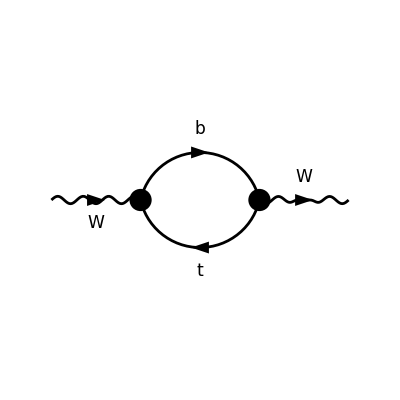

```mathematica
Paint[diagWselfE,ColumnsXRows -> {1, 1},SheetHeader->None,
Numbering -> None,ImageSize->{150,150}];
```

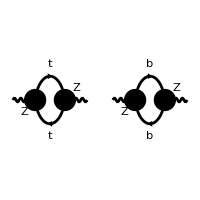

```mathematica
Paint[diagZselfE,ColumnsXRows -> {2, 1},SheetHeader->None,
Numbering -> None,ImageSize->{200,200}];
```

```mathematica
ampWselfE=3*FCFAConvert[CreateFeynAmp[diagWselfE,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
ampZselfE=3*FCFAConvert[CreateFeynAmp[diagZselfE,Truncated->True],IncomingMomenta->{q},OutgoingMomenta->{q},LorentzIndexNames-> {μ,ν}, LoopMomenta->{l},List->False,DropSumOver->True,SMP->True,UndoChiralSplittings->True]//Contract//FCTraceFactor;
```

```mathematica
ampWselfE = ChangeDimension[ampWselfE/.DiracTrace->TR//Simplify,D];
ampZselfE = ChangeDimension[ampZselfE/.DiracTrace->TR//Simplify,D];
```

```mathematica
ReducedWSelfE = TID[ampWselfE,l,ToPaVe->True];
ReducedZSelfE = TID[ampZselfE,l,ToPaVe->True];
```

```mathematica
ZSelfET = Simplify[Contract[Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]/D,ReducedZSelfE]];
WSelfET = Simplify[Contract[Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]/D,ReducedWSelfE]];
```

```mathematica
SPD[q,q]=0;
```

```mathematica
answer = PaXEvaluate[(ZSelfET*SMP["cos_W"]^2)/SMP["m_W"]^2 - WSelfET/SMP["m_W"]^2]//FCHideEpsilon
```

(3 e^2 (2 m_b^2 m_t^2 log(m_b^2/m_t^2)-m_b^4+m_t^4))/(64 π^2 m_W^2 (m_b^2-m_t^2) (sin(θ_W))^2)

```mathematica
seriesanswer = Series[answer/.SMP["m_b"]->ϵ*SMP["m_t"],{ϵ,0,1}]
```

-(3 (e^2 m_t^2))/(64 (π^2 m_W^2 (sin(θ_W))^2))+O(ϵ^2)

```mathematica
seriesanswer/.SMP["e"]->SMP["g_W"]*SMP["sin_W"]/.SMP["g_W"]-> Sqrt[8*SMP["G_F"]/Sqrt[2](SMP["m_W"])^2]
```

-(3 (G_F m_t^2))/(8 (√2 π^2))+O(ϵ^2)

```mathematica
(*ϵ = Subscript[m, b]/Subscript[m, t]*)
```

```mathematica
(*This is -1 times the usual answer, indicating some sign error within feyncalc???*)
```